## Nucleation Analysis (Multi - stranded)

/Users/htailor/Desktop/lapack_collagen/results

L: | 20.25
m: | 40
kappa: | 0.1
sigma: | 0.001
kappa_sigma_r: | 100.
Delta: | 0.25
Extension Minimum: | 0
Extension Maximum: | 50
e0: | 0.01875
beta: | 38.6817

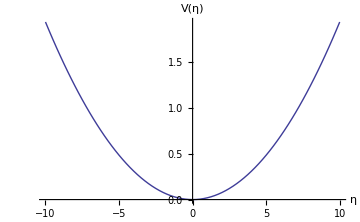

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]

PotentialData = Import["potential_data.out","Table"];
PartitionFunction=Import["PartitionFunction_0_0.out","Table"];
FreeEnergy=Import["FreeEnergy_0_0.out","Table"];
dPartitionFunction=Import["dPartitionFunction_0_0.out","Table"];
dFreeEnergy=Import["dFreeEnergy_0_0.out","Table"];
Parameters=Import["Parameters","Grid"]
Needs["PlotLegends`"]
PlotPotentialData=ListLinePlot[{PotentialData},ImageSize->Medium,AxesOrigin->{0,0},AxesLabel->{Style["η",FontSize->18],Style["V(η)",FontSize->18]},PlotStyle->Thick,PlotRange->All]
```

Numerical Results - Partition Function

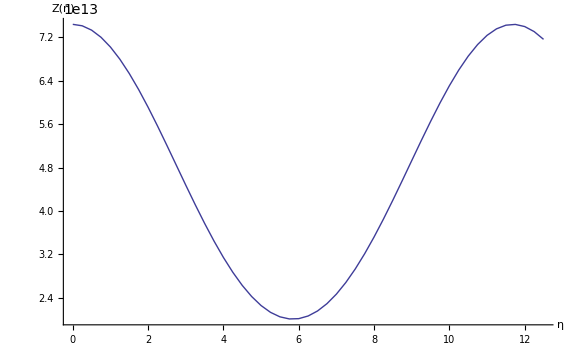

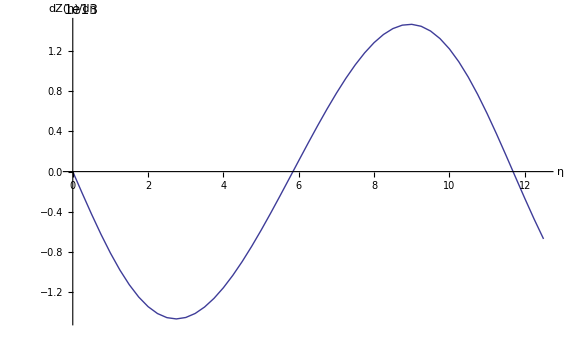

```mathematica
PartitionFunction;
PlotGraph1=ListLinePlot[{PartitionFunction},ImageSize->Large,AxesOrigin->{0,0},AxesLabel->{Style["η",FontSize->18],Style["Z(η)",FontSize->18]},PlotStyle->Thick,PlotRange->All]

dPartitionFunction;
PlotGraph1=ListLinePlot[{dPartitionFunction},ImageSize->Large,AxesOrigin->{0,0},AxesLabel->{Style["η",FontSize->18],Style["dZ(η)/dη",FontSize->18]},PlotStyle->Thick,PlotRange->All]
```

Numerical Results - Free Energy

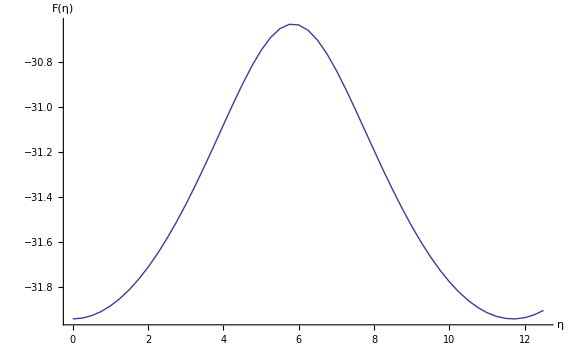

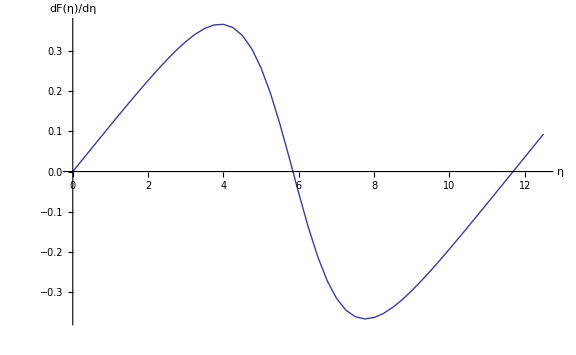

```mathematica
FreeEnergy;
PlotGraph1=ListLinePlot[{FreeEnergy},ImageSize->Large,AxesOrigin->{0,0},PlotStyle->Thick,AxesLabel->{Style["η",FontSize->18],Style["F(η)",FontSize->18]},PlotRange->All]

dFreeEnergy;
PlotGraph1=ListLinePlot[{dFreeEnergy},ImageSize->Large,AxesOrigin->{0,0},PlotStyle->Thick,AxesLabel->{Style["η",FontSize->18],Style["dF(η)/dη",FontSize->18]},PlotRange->All]
```